```mathematica
T=π;
ReLU[x_]=Piecewise[{{0,x<0}},x];
PeReLU[x_]=ReLU[Mod[x+T,2*T]-T];
```

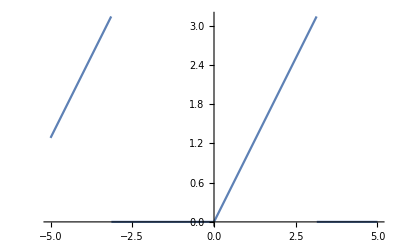

```mathematica
Plot[PeReLU[x],{x,-5,5}]
```

```mathematica
ManualPeReLUFS[K_]=π/4+Sum[(T*(-1)^k-T)/(k^2*π^2)*Cos[k*π*y/T]-T*(-1)^k/(k*π)*Sin[k*π*y/T],{k,1,K}];
ManualPeReLUFS1=PeReLUFS[1];
ManualPeReLUFS2=ManualPeReLUFS[2];
ManualPeReLUFS4=ManualPeReLUFS[4];
```

```mathematica
PeReLUFS[N_]=FourierTrigSeries[PeReLU[y],y,N];
PeReLUFS1=PeReLUFS[1];
PeReLUFS2=PeReLUFS[2];
PeReLUFS4=PeReLUFS[4];
```

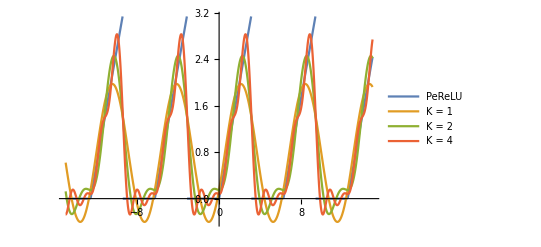

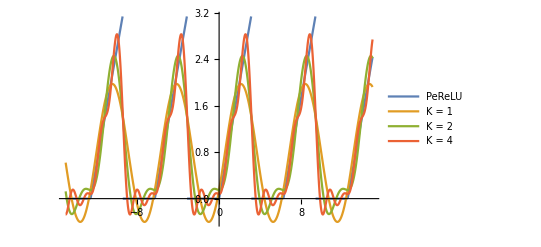

```mathematica
Plot[
{PeReLU[x],PeReLUFS1/.y->x,PeReLUFS2/.y->x,PeReLUFS4/.y->x},
{x,-15,15},
PlotLegends->{"PeReLU", "K = 1", "K = 2", "K = 4"}
]
Plot[
{PeReLU[x],ManualPeReLUFS1/.y->x,ManualPeReLUFS2/.y->x,ManualPeReLUFS4/.y->x},
{x,-15,15},
PlotLegends->{"PeReLU", "K = 1", "K = 2", "K = 4"}
]
```

```mathematica
FourierCosSeries[PeReLU[y],y,8]
```

π/2-(4 Cos[y])/π-(4 Cos[3 y])/(9 π)-(4 Cos[5 y])/(25 π)-(4 Cos[7 y])/(49 π)

```mathematica
FullSimplify[Integrate[1/T*ReLU[x]*Cos[k*π*x/T],{x,-T,T},Assumptions->{k∈Integers,x∈Reals,T∈Reals,T>0}],{k∈Integers,x∈Reals}]
FullSimplify[Integrate[1/T*ReLU[x]*Sin[k*π*x/T],{x,-T,T},Assumptions->{k∈Integers,x∈Reals,T∈Reals,T>0}],{k∈Integers,x∈Reals}]
```

((-1+(-1)^k) T)/(k^2 π^2)

((-1)^(1+k) T)/(k π)

```mathematica
FullSimplify[FourierCosCoefficient[ReLU[x],x,k],{k∈Integers,x∈Reals}]
FullSimplify[FourierSinCoefficient[ReLU[x],x,k],{k∈Integers,x∈Reals}]
```

(2 (-1+(-1)^k))/(k^2 π)

-(2 (-1)^k)/k

```mathematica
PeReLUFS4
π/4+Sum[(T*(-1)^k-T)/(k^2*π^2)*Cos[k*π*y/T]-T*(-1)^k/(k*π)*Sin[k*π*y/T],{k,1,4}]
```

π/4-(2 Cos[y])/π-(2 Cos[3 y])/(9 π)+Sin[y]-1/2 Sin[2 y]+1/3 Sin[3 y]-1/4 Sin[4 y]

π/4-(2 Cos[y])/π-(2 Cos[3 y])/(9 π)+Sin[y]-1/2 Sin[2 y]+1/3 Sin[3 y]-1/4 Sin[4 y]

```mathematica
Integral[Tanh[x]*Cos[k*π*x/T],{x,-T,T},Assumptions->{k∈Integers,x∈Reals,T∈Reals,T>0}]
```

Integral[Cos[(k π x)/T] Tanh[x],{x,-T,T},Assumptions→{k∈ℤ,x∈ℝ,T∈ℝ,T>0}]

```mathematica
Integral[Tanh[x]*Sin[a*x],{x,0,T}]]
```

Integral[Sin[a x] Tanh[x],{x,0,T}]

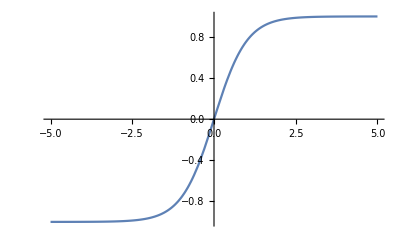

```mathematica
Plot[Tanh[x],{x,-5,5}]
```

```mathematica
D[D[D[Tanh[x],x],x],x]
```

-2 Sech[x]^4+4 Sech[x]^2 Tanh[x]^2

```mathematica
Limit[Series[Tanh[x],{x,0,k}],k->∞]
```

Series::serlim: Series order specification k is not a machine-sized integer.

lim_(k→∞) Series[Tanh[x],{x,0,k}]

```mathematica
Series[Tanh[x],x->0]
```

x+O[x]^2

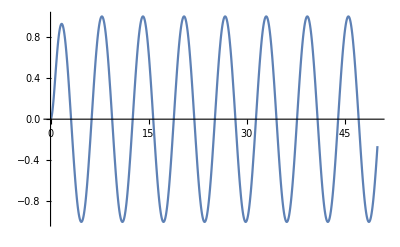

```mathematica
Plot[Tanh[x]*Sin[x],{x,0,50}]
```

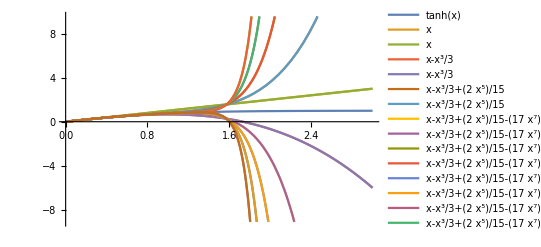

```mathematica
Plot[{Tanh[x],Evaluate[Table[Normal[Series[Tanh[x],{x,0,n}]],{n,20}]]},{x,0,3},PlotLegends->"Expressions"]
```

```mathematica
PeTanh[x_]=Tanh[(Mod[x+T,2*T]-T)/2];
```

```mathematica
TanhFS[N_]=FourierTrigSeries[Tanh[y/2],y,N];
TanhFS1=TanhFS[1];
TanhFS2=TanhFS[2];
TanhFS4=TanhFS[4];
TanhFS8=TanhFS[8];
```

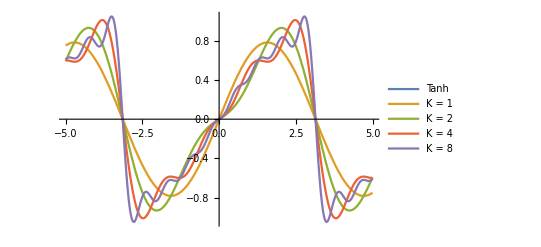

```mathematica
Plot[
{PeTanh[x],TanhFS1/.y->x,TanhFS2/.y->x,TanhFS4/.y->x,TanhFS8/.y->x},
{x,-5,5},
PlotLegends->{"Tanh", "K = 1", "K = 2", "K = 4", "K = 8"}
]
```

```mathematica
FourierCosCoefficient[Tanh[x],x,5]
```

1/π 2 (1/290 ⅈ (29 (Hypergeometric2F1[-(5 ⅈ)/2,1,1-(5 ⅈ)/2,-ⅇ^(2 π)]-Hypergeometric2F1[(5 ⅈ)/2,1,1+(5 ⅈ)/2,-ⅇ^(2 π)])+5 ⅇ^(2 π) ((-5+2 ⅈ) Hypergeometric2F1[1,1-(5 ⅈ)/2,2-(5 ⅈ)/2,-ⅇ^(2 π)]+(5+2 ⅈ) Hypergeometric2F1[1,1+(5 ⅈ)/2,2+(5 ⅈ)/2,-ⅇ^(2 π)]))+1/4 (-PolyGamma[0,-(5 ⅈ)/4]-PolyGamma[0,(5 ⅈ)/4]+PolyGamma[0,1/2-(5 ⅈ)/4]+PolyGamma[0,1/2+(5 ⅈ)/4]))

```mathematica
LinearTanh[x_]=Piecewise[{{-1,-π/4>x},{2*x/(π/2),-π/4≤x≤π/4},{1,x>π/4}}];
LinearTanhFS1=FourierTrigSeries[LinearTanh[y],y,1];
LinearTanhFS2=FourierTrigSeries[LinearTanh[y],y,2];
LinearTanhFS4=FourierTrigSeries[LinearTanh[y],y,4];
LinearTanhFS8=FourierTrigSeries[LinearTanh[y],y,8];
```

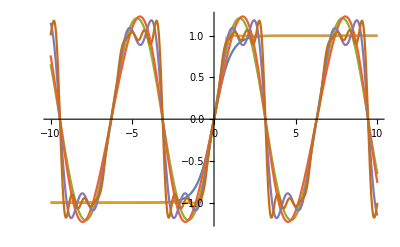

```mathematica
Plot[{Tanh[x],LinearTanh[x],LinearTanhFS1/.y->x,LinearTanhFS2/.y->x,LinearTanhFS4/.y->x,LinearTanhFS8/.y->x},{x,-10,10}]
```

```mathematica
FourierTrigSeries[LinearTanh[y],y,1]
```

(2 (2+π) Sin[y])/π^2

```mathematica
N[FourierCosCoefficient[Tanh[x],x,8]]
```

-0.0102451+0. ⅈ

```mathematica
Sigmoid[x_]=1/(1+E^(-x));
TanhApprox[x_]=x/Sqrt[1+x^2];
```

```mathematica
FullSimplify[FourierTrigSeries[Sigmoid[x],x,5]]
```

1/(60 π)(-60 (-1+π Csch[π]+Hypergeometric2F1[-ⅈ,1,1-ⅈ,-ⅇ^π]+Hypergeometric2F1[ⅈ,1,1+ⅈ,-ⅇ^π]-Cos[x] (-1+Hypergeometric2F1[-2 ⅈ,1,1-2 ⅈ,-ⅇ^π]+Hypergeometric2F1[2 ⅈ,1,1+2 ⅈ,-ⅇ^π]-π Csch[π] Sech[π])) Sin[x]+5 (6 π-4 (-1+3 π Csch[3 π]+Hypergeometric2F1[-3 ⅈ,1,1-3 ⅈ,-ⅇ^π]+Hypergeometric2F1[3 ⅈ,1,1+3 ⅈ,-ⅇ^π]) Sin[3 x]+3 (-1-4 π Csch[4 π]+Hypergeometric2F1[-4 ⅈ,1,1-4 ⅈ,-ⅇ^π]+Hypergeometric2F1[4 ⅈ,1,1+4 ⅈ,-ⅇ^π]) Sin[4 x])-12 (-1+5 π Csch[5 π]+Hypergeometric2F1[-5 ⅈ,1,1-5 ⅈ,-ⅇ^π]+Hypergeometric2F1[5 ⅈ,1,1+5 ⅈ,-ⅇ^π]) Sin[5 x])

```mathematica
FullSimplify[FourierTrigSeries[Erf[x],x,5]]
```

1/(2 π)(4 Erf[π] Sin[x]+(2 ⅈ (Erfi[1/2-ⅈ π]-Erfi[1/2+ⅈ π]) Sin[x])/ⅇ^(1/4)+((-2 ⅇ Erf[π]+ⅈ (Erfi[1-ⅈ π]-Erfi[1+ⅈ π])) Sin[2 x])/ⅇ+4/3 Erf[π] Sin[3 x]+(2 ⅈ (Erfi[3/2-ⅈ π]-Erfi[3/2+ⅈ π]) Sin[3 x])/(3 ⅇ^(9/4))+1/2 (-2 Erf[π]+(ⅈ (Erfi[2-ⅈ π]-Erfi[2+ⅈ π]))/ⅇ^4) Sin[4 x]+4/5 Erf[π] Sin[5 x]+(2 ⅈ (Erfi[5/2-ⅈ π]-Erfi[5/2+ⅈ π]) Sin[5 x])/(5 ⅇ^(25/4)))

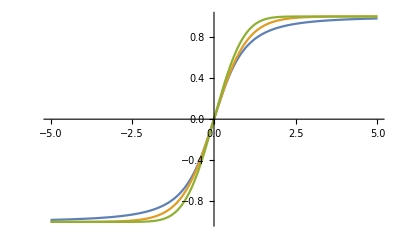

```mathematica
Plot[{TanhApprox[x],Tanh[x],Erf[x]},{x,-5,5}]
```

```mathematica
FourierTrigSeries[TanhApprox[x],x,1]
```

FourierTrigSeries[x/(√(1+x^2)),x,1]

```mathematica
Integrate[TanhApprox[x]*Sin[k*π*x/T],{x,-T,T},Assumptions->{k∈Integers,T∈Reals,T>0,x∈Reals}]
```

Integrate[(x Sin[(k π x)/T])/(√(1+x^2)),{x,-T,T},Assumptions→{k∈ℤ,T∈ℝ,T>0,x∈ℝ}]

```mathematica
FourierSinCoefficient[TanhApprox[x],x,1]
```

FourierSinCoefficient[x/(√(1+x^2)),x,1]

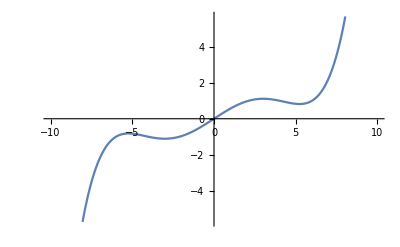

```mathematica
Plot[InterpolatingPolynomial[{{-6,Tanh[-6]},{-4,Tanh[-4]},{-2,Tanh[-2]},{0,Tanh[0]},{2,Tanh[2]},{4,Tanh[4]},{6,Tanh[6]}},y]/.y->x,{x,-10,10}]
```

```mathematica
fHat[x_,a9_,a8_,a7_,a6_,a5_,a4_,a3_,a2_,a1_,a0_]=a9*x^9+a8*x^8+a7*x^7+a6*x^6+a5*x^5+a4*x^4+a3*x^3+a2*x^2+a1*x+a0;
fHatPrime[x_,a9_,a8_,a7_,a6_,a5_,a4_,a3_,a2_,a1_,a0_]=9a9*x^8+8a8*x^7+7a7*x^6+6a6*x^5+5a5*x^4+4a4*x^3+3a3*x^2+2a2*x+a1;
```

```mathematica
Solve[{
fHat[-5,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==-1,
fHat[+5,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==+1,
fHat[-3,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==-0.9950547536867305,
fHat[+3,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==+0.9950547536867305,
fHat[+0,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==0,
fHatPrime[-5,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==0,
fHatPrime[+5,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==0,
fHatPrime[-3,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==0.00986603716544019,
fHatPrime[+3,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==0.00986603716544019,
fHatPrime[+0,a9,a8,a7,a6,a5,a4,a3,a2,a1,a0]==1
},{a9,a8,a7,a6,a5,a4,a3,a2,a1,a0}]
```

{{a9→8.21138×10^-6,a8→-2.40934×10^-20,a7→-0.000579539,a6→4.799×10^-19,a5→0.0147006,a4→1.16789×10^-17,a3→-0.165606,a2→-3.11963×10^-16,a1→1.,a0→0.}}

```mathematica
fHatT[x_]=Piecewise[{{fHat[x,8.21137993691547*^-6,-2.4093381610788962*^-20,-0.0005795387262191688,4.799003089577444*^-19,0.014700598929241932,1.1678909606381139*^-17,-0.1656060808583721,-3.119629002251367*^-16,1.0000000000000007,0.],-5≤x≤5}},Sign[x]]
```

Piecewise[{{0.+1. x-3.11963×10^-16 x^2-0.165606 x^3+1.16789×10^-17 x^4+0.0147006 x^5+4.799×10^-19 x^6-0.000579539 x^7-2.40934×10^-20 x^8+8.21138×10^-6 x^9, -5≤x≤5}, {Sign[x], True}}]

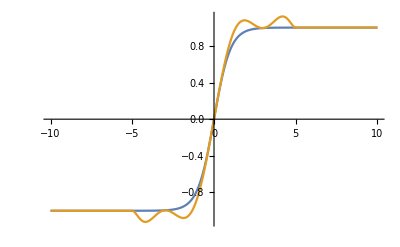

```mathematica
Plot[{Tanh[x],fHatT[x]},{x,-10,10}]
```